```mathematica
(* 0/90  Laminate
This notebook calculates the exact value of kx, ky and kxy for a given material data
The values of the curvatures compare well with the FE *)
```

```mathematica
Astar0={{((1+β)*k)/(E0*t),(-2*β*ν*k)/(E0*t),0},{(-2*β*ν*k)/(E0*t),((1+β)*k)/(E0*t),0},{0,0,1/(2*E0*γ*t)}};
Bstar0={{-0.5*t*k*(β^2-1),-t*β*ν*k*(β-1),0},{t*β*ν*k*(β-1),0.5*t*k*(β^2-1),0},{0,0,0}};
(*Bstar0={{0.5*t*k*(β^2-1),t*β*ν*k*(β-1),0},{-t*β*ν*k*(β-1),-0.5*t*k*(β^2-1),0},{0,0,0}};*)
(*Dstar0={{(E0*t^3/12)*k*β*(β-1)*(1-β*ν^2),8*E0*t^3*k*β^2*ν*(1-β*ν^2),0},{8*E0*t^3*k*β^2*ν*(1-β*ν^2),4*E0*t^3*k*β*(β-1)*(1-β*ν^2),0},{0,0,2*E0*t^3*γ}};*)
Dstar0={{ (E0*t^3/12)*k*(1+β)*(1+14* β+β^2-16*ν^2*β^2),(E0*t^3/6)*k*β*ν*(1+14* β+β^2-16*ν^2*β^2),0},{(E0*t^3/6)*k*β*ν*(1+14* β+β^2-16*ν^2*β^2),(E0*t^3/12)*k*(1+β)*(1+14* β+β^2-16*ν^2*β^2),0},{0,0,(2/3)*E0*t^3*γ}};
```

```mathematica
Nvec={{Nx[x,y]},{Ny[x,y]},{Nxy[x,y]}};
AstN=Astar0.Nvec;
ϕ= s*(a^2*y^4)/(4 b^2)+s*(b^2*x^4)/(4 a^2)+s*(x^2*y^2)/2-s*(a^2*y^2)/2-s*(b^2*x^2)/2;
ssol=Solve[k*(1+β)*D[ϕ,{x,4}]+((1/(2*γ))-4*k*β*ν)*D[D[ϕ,{x,2}],{y,2}]+k*(1+β)*D[ϕ,{y,4}]==E0*t*g,s];
ψ0=(a^2 b^2*γ)/(a^2 b^2+6 a^4 k γ+6 b^4 k γ+6 a^4 k β γ+6 b^4 k β γ-8 a^2 b^2 k β γ ν) //FullSimplify;
s0=E0*g*t*ψ0;
k*(1+β)*D[ϕ,{x,4}]+((1/(2*γ))-4*k*β*ν)*D[D[ϕ,{x,2}],{y,2}]+k*(1+β)*D[ϕ,{y,4}]/.{s-> s0}//Simplify//Chop;
```

```mathematica
ψ00=(a^2 b^2*γ)/(a^2 b^2+6 a^4 k γ+6 b^4 k γ+6 a^4 k β γ+6 b^4 k β γ-8 a^2 b^2 k β γ ν) //FullSimplify;
```

```mathematica
Nx=s*(x^2+(3 a^2*y^2)/b^2-a^2);
Ny=s*(y^2+(3 b^2*x^2)/a^2-b^2);
Nxy=-2*s*x*y;
Nvec={{Nx},{Ny},{Nxy}}/.{s->s0};
kvec={{kxx},{kyy},{2*kxy}};
Nxxth=-E0*ΔT*t*(α11+β*α22+ν*β*(α11+α22));
Nyyth=Nxxth;
Nxyth=0;
Mxxth=-0.5*E0*ΔT*t^2*(-α11+β*α22+ν*β*(α11-α22));
Myyth=-Mxxth;
Mxyth=0;
Nthvec={{Nxxth},{Nyyth},{Nxyth}};
Mthvec={{Mxxth},{Myyth},{Mxyth}};
```

```mathematica
(* Activate this part for calculating T1 and T2 *)
(*kvec={{kxx},{kyy},{2*kxy}};
Nxxth=-E0*ΔT*t*(α11+β*α22+ν*β*(α11+α22));
Nyyth=Nxxth;
Nxyth=0;
Mxxth=-0.5*E0*ΔT*t^2*(-α11+β*α22+ν*β*(α11-α22));
Myyth=-Mxxth;
Mxyth=0;
Nthvec={{Nxxth},{Nyyth},{Nxyth}};
Mthvec={{Mxxth},{Myyth},{Mxyth}};
ThermalEn=0.5*Transpose[Nthvec].Astar0.Nthvec+Transpose[Nthvec].Bstar0.kvec+Transpose[Mthvec].kvec//Expand// Rationalize//Simplify;
ThermalEnS=Integrate[ThermalEn[[1,1]],{x,y}∈Disk[{0,0},{a,b}]]//Expand// Rationalize//FullSimplify;*)
```

```mathematica
MemEn=0.5*Transpose[Nvec].Astar0.Nvec/. { g-> kxx*kyy-kxy*kxy}//Expand // Rationalize//Simplify;
MemtotS= Integrate[MemEn[[1,1]],{x,y}∈Disk[{0,0},{a,b}]]//Expand// Rationalize//Simplify;
BendEn= 0.5*Transpose[kvec].Dstar0.kvec//Expand// Rationalize//Simplify;
BendEnS=Integrate[BendEn[[1,1]],{x,y}∈Disk[{0,0},{a,b}]];
ThermalEn=0.5*Transpose[Nthvec].Astar0.Nthvec+Transpose[Nthvec].Bstar0.kvec+Transpose[Mthvec].kvec//Expand// Rationalize//Simplify;
ThermalEnS=Integrate[ThermalEn[[1,1]],{x,y}∈Disk[{0,0},{a,b}]]//Expand// Rationalize//FullSimplify;
Q0m =E0m* {{1, βm*νm,0},{βm*νm,βm,0},{0,0,γm}};
Q90m =E0m* {{βm, βm*νm,0},{βm*νm,1,0},{0,0,γm}};
σm0 = Q0m.(zm*kvec); σm90 = Q90m.(zm*kvec);
EnMFCS=Am*( Integrate[Transpose[σm90].(zm*kvec)/2, {zm,-tm-t,-t}])//Expand//Simplify;
U=0.5*Transpose[Nvec].Astar0.Nvec + 0.5*Transpose[kvec].Dstar0.kvec-0.5*Transpose[Nthvec].Astar0.Nthvec-Transpose[Nthvec].Bstar0.kvec-Transpose[Mthvec].kvec /. {ψ-> ψ00, g-> kxx*kyy-kxy*kxy}//Expand// Rationalize//Simplify;
Utot=Integrate[U,{x,y}∈Disk[{0,0},{a,b}]]//Rationalize//Expand//Simplify;
Utot2= Utot + EnMFCS;
```

```mathematica
Transpose[σm0]
```

{{E0m kxx zm+E0m kyy zm βm νm,E0m kyy zm βm+E0m kxx zm βm νm,2 E0m kxy zm γm}}

```mathematica
Clear[ψ0]
```

```mathematica
(* Membrane energy*)
d11=Dstar0[[1,1]]*12/(-E0*t^3);
Usc= -a*b*E0* π*t^3*d11/(√ψ0*12);
MemEnSc=(1/2)*ϕt*(kxy0^2-kxx0*kyy0)^2;
MemEnS0 = MemEnSc*Usc/.{kxx0-> kxx*(ψ0)^(1/4), kyy0-> kyy*(ψ0)^(1/4), kxy0-> kxy*(ψ0)^(1/4),ϕt-> -a^2*b^2 √ψ0/(t^2 *d11)}//Expand// Rationalize//FullSimplify ;
MemtotS-MemEnS0 /. {ψ0-> ψ0 , g-> kxx*kyy-kxy*kxy}//Expand// Rationalize//Simplify  //Chop
```

ConditionalExpression[-(a^3 b^3 E0 (kxy^2-kxx kyy)^2 π t (6 a^4 k (1+β) γ ψ0+6 b^4 k (1+β) γ ψ0+a^2 b^2 (ψ0-γ (1+8 k β ν ψ0))))/(24 (6 a^4 k (1+β) γ+6 b^4 k (1+β) γ+a^2 b^2 (1-8 k β γ ν))),a>0&&b>0]

```mathematica
(* Bending energy*)
Dnd = {{1,μ,0},{μ,1,0},{0,0,ρ}};
kvec0={{kxx0},{kyy0},{2*kxy0}};
BendEnSc=(1/2)*Transpose[kvec0].Dnd.kvec0;
BendEnS0= BendEnSc*Usc/.{kxx0-> kxx*(ψ0)^(1/4), kyy0-> kyy*(ψ0)^(1/4), kxy0-> kxy*(ψ0)^(1/4) , μ-> (2 β ν)/(1+β) , ρ -> (-8 γ)/(k (1+β) (-1-14 β+β^2 (-1+16 ν^2)))}//Expand// Rationalize//Simplify ;
BendEnS - BendEnS0//Expand// Rationalize//Simplify  //Chop
```

{{ConditionalExpression[0,a>0&&b>0]}}

```mathematica
(* Thermal energy*)
T1=(-2 k ΔT (α11+α11 β ν+α22 β (1+ν))^2 (-1+β (-1+2 ν)))*(-6*√ψ0/(t^3*d11));
(*T2 = (α22 β (1-ν+k (-1+β) (1+ν) (-1-β+2 β ν))+α11 (-1+β ν+k (-1+β) (-1+β (-1+ν)+β^2 ν (-1+2 ν))))*(-6*√ψ0/t^3)/(ψ0)^(1/4);*)
(*T2 = (-α22 β (-1+ν+k (-1+β) (1+ν) (-1-β+2 β ν))+α11 (-1+β ν-k (-1+β) (1+β ν) (-1-β+2 β ν)))*(-6*√ψ0/(t^3*d11))/(ψ0)^(1/4);*)
T2 = (-α22 β (1-ν+k (-1+β) (1+ν) (-1-β+2 β ν))+α11 (1-β ν-k (-1+β) (1+β ν) (-1-β+2 β ν)))*(-6*√ψ0/(t^3*d11))/(ψ0)^(1/4);
ThermalEnSc = t*ΔT* (T1 + kyy0*t*(-T2) + kxx0*t*T2);
ThermalEnS0=ThermalEnSc*Usc/.{kxx0-> kxx*(ψ0)^(1/4), kyy0-> kyy*(ψ0)^(1/4), kxy0-> kxy*(ψ0)^(1/4) }//Expand//Simplify ;
ThermalEnS - ThermalEnS0//Expand// Rationalize//Simplify  //Chop
```

0

```mathematica
(*Bonding of MFC*)
(*Actual Form*)
Q0m =E0m* {{1, βm*νm,0},{βm*νm,βm,0},{0,0,γm}};
Q90m =E0m* {{βm, βm*νm,0},{βm*νm,1,0},{0,0,γm}};
σm0 = Q0m.(zm*kvec); σm90 = Q90m.(zm*kvec);
EnMFCS90=Am*(Integrate[Transpose[σm90].(zm*kvec)/2, {zm,t,tm+t}])//Expand//Simplify
```

{{1/6 Am E0m tm (3 t^2+3 t tm+tm^2) (kyy^2+kxx^2 βm+4 kxy^2 γm+2 kxx kyy βm νm)}}

```mathematica
(*σm0 = Q0m.(zm*kvec); σm90 = Q90m.(zm*kvec);*)
```

```mathematica
(*Bonding of MFC*)
(*Non-Dimensional Form*)
ϕb0=-(4 Am E0m)/(a b E0 k π t^3 (1+β) (-1-14 β+β^2 (-1+16 ν^2)));
EnMFCSc= (1/2)*ϕb0*tm (3 t^2+3 t tm+tm^2)*(kxx0^2 (1+βm)+kyy0^2 (1+βm)+8 kxy0^2 γm+4 kxx0 kyy0 βm νm);
EnMFCSc90= (1/2)*ϕb0*tm (3 t^2+3 t tm+tm^2)*(kyy0^2+kxx0^2 βm+4 kxy0^2 γm+2 kxx0 kyy0 βm νm);
```

```mathematica
EnMFCS90-EnMFCSc90*Usc/.{kxx0-> kxx*(ψ0)^(1/4), kyy0-> kyy*(ψ0)^(1/4), kxy0-> kxy*(ψ0)^(1/4) }//Expand//Simplify //Chop
```

{{0}}

```mathematica
(*Total Strain Energy*)
UtotSc= MemEnSc + BendEnSc - ThermalEnSc /.{kxx0-> kxx*(ψ0)^(1/4), kyy0-> kyy*(ψ0)^(1/4), kxy0-> kxy*(ψ0)^(1/4),ϕt-> -a^2*b^2 √ψ0/(t^2 *d11) , μ-> (2 β ν)/(1+β) , ρ -> (-8 γ)/(k (1+β) (-1-14 β+β^2 (-1+16 ν^2)))}//Expand//Simplify //Chop;
(Utot-UtotSc*Usc/.{kxx0-> kxx*(ψ0)^(1/4), kyy0-> kyy*(ψ0)^(1/4), kxy0-> kxy*(ψ0)^(1/4),ϕt-> -a^2*b^2 √ψ0/(t^2 *d11) , μ-> (2 β ν)/(1+β) , ρ -> (-8 γ)/(k (1+β) (-1-14 β+β^2 (-1+16 ν^2)))})//Expand//Simplify //Chop
```

{{0}}

```mathematica
Q0m =E0m* {{1, βm*νm,0},{βm*νm,βm,0},{0,0,γm}};
Q90m =E0m* {{βm, βm*νm,0},{βm*νm,1,0},{0,0,γm}};
(*σm0 = Q0m.(zm*kvec);*)
 σm90 = Q90m.(zm*kvec);
EnMFCS=Am*(Integrate[Transpose[σm90].(zm*kvec)/2, {zm,t,t + tm}])//Expand//Simplify;
Utot2= Utot + EnMFCS;
```

```mathematica
Utot2v=Utot2/.{E0m-> E0m0, tm-> tm0,Am-> 0.5*Am0, βm-> βm0,γm-> γm0, νm-> νm0}//Simplify
```

{{ConditionalExpression[(a b E0 π t (-a^2 b^2 (-1+8 k β γ ν) (4 t (8 kxy^2 t γ-3 (kxx-kyy) ΔT (α11+α22 β (-1+ν)-α11 β ν))+k (-12 kyy t (-1+β) ΔT (α11+α11 β ν+α22 β (1+ν)) (-1+β (-1+2 ν))+24 ΔT^2 (α11+α11 β ν+α22 β (1+ν))^2 (-1+β (-1+2 ν))-kxx^2 t^2 (1+β) (-1-14 β+β^2 (-1+16 ν^2))-kyy^2 t^2 (1+β) (-1-14 β+β^2 (-1+16 ν^2))-4 kxx t (-3 α11 (-1+β) ΔT (-1+β (-1+ν)+β^2 ν (-1+2 ν))-β (3 α22 (-1+β) ΔT (1+ν) (-1-β+2 β ν)+kyy t ν (1+14 β+β^2-16 β^2 ν^2)))))-6 b^4 k (1+β) γ (-4 t (8 kxy^2 t γ-3 (kxx-kyy) ΔT (α11+α22 β (-1+ν)-α11 β ν))+k (12 kyy t (-1+β) ΔT (α11+α11 β ν+α22 β (1+ν)) (-1+β (-1+2 ν))-24 ΔT^2 (α11+α11 β ν+α22 β (1+ν))^2 (-1+β (-1+2 ν))+kxx^2 t^2 (1+β) (-1-14 β+β^2 (-1+16 ν^2))+kyy^2 t^2 (1+β) (-1-14 β+β^2 (-1+16 ν^2))+4 kxx t (-3 α11 (-1+β) ΔT (-1+β (-1+ν)+β^2 ν (-1+2 ν))-β (3 α22 (-1+β) ΔT (1+ν) (-1-β+2 β ν)+kyy t ν (1+14 β+β^2-16 β^2 ν^2)))))+a^4 γ (b^4 (kxy^2-kxx kyy)^2-6 k (1+β) (-4 t (8 kxy^2 t γ-3 (kxx-kyy) ΔT (α11+α22 β (-1+ν)-α11 β ν))+k (12 kyy t (-1+β) ΔT (α11+α11 β ν+α22 β (1+ν)) (-1+β (-1+2 ν))-24 ΔT^2 (α11+α11 β ν+α22 β (1+ν))^2 (-1+β (-1+2 ν))+kxx^2 t^2 (1+β) (-1-14 β+β^2 (-1+16 ν^2))+kyy^2 t^2 (1+β) (-1-14 β+β^2 (-1+16 ν^2))+4 kxx t (-3 α11 (-1+β) ΔT (-1+β (-1+ν)+β^2 ν (-1+2 ν))-β (3 α22 (-1+β) ΔT (1+ν) (-1-β+2 β ν)+kyy t ν (1+14 β+β^2-16 β^2 ν^2))))))))/(24 (6 a^4 k (1+β) γ+6 b^4 k (1+β) γ+a^2 b^2 (1-8 k β γ ν)))+0.0833333 Am0 E0m0 tm0 (3 t^2+3 t tm0+tm0^2) (kyy^2+kxx^2 βm0+4 kxy^2 γm0+2 kxx kyy βm0 νm0),a>0&&b>0]}}

```mathematica
E11 = 140*10^9;E22 = 13*10^9; 
ν= 0.3; G12 = 6.6*10^9; t = 0.149*10^-3;
α11 = -8*10^-7 ; α22 = 2.9*10^-5 ;
(*ΔT= 120;*)
```

```mathematica
β = E22/E11; E0 = E11/(1-ν^2*β); γ = G12/E0;
k = 1/(1 + 2*β + β^2-4*β^2*ν^2);
k1 = 1 + 14*β + β^2-16*ν^2;
a = 0.075; b = 0.05;
```

```mathematica
tm0= 0.29*10^-3;
E11m0 = 28.6*10^9;E22m0 = 13.1*10^9; G12m0 = 6.6*10^9;
νm0= 0.29; βm0= E22m0/E11m0; Lm0= 28*10^-3; Wm0=85*10^-3; Am0=Lm0*Wm0;
E0m0 = E11m0/(1-νm0^2*βm0);  γm0 = G12m0/E0m0*νm0;
```

```mathematica
eq1=D[Utot,kxx];
eq2=D[Utot,kyy];
eq3=D[Utot,kxy];
```

```mathematica
Utot//Simplify
```

{{0.000342944 kxy^2+0.0040296 kxy^4+0.000482924 kyy^2+kxx^2 (0.000482924+0.0040296 kyy^2)+kxx ((0.0000492393-0.00805921 kxy^2) kyy+0.0000882176 ΔT)-0.0000882176 kyy ΔT-1.5479×10^-6 ΔT^2}}

```mathematica
Utot = Utot//Simplify
```

{{0.000342944 kxy^2+0.0040296 kxy^4+0.000482924 kyy^2+kxx^2 (0.000482924+0.0040296 kyy^2)+kxx ((0.0000492393-0.00805921 kxy^2) kyy+0.0000882176 ΔT)-0.0000882176 kyy ΔT-1.5479×10^-6 ΔT^2}}

```mathematica
soln=NSolve[{eq1[[1,1,1]]==0 &&eq2[[1,1,1]]==0&&eq3[[1,1,1]]==0},{kxx,kyy,kxy}]
```

{{kxx→0.,kyy→0.,kxy→0.}}

```mathematica
eq1=D[Utot2v,kxx];
eq2=D[Utot2v,kyy];
eq3=D[Utot2v,kxy];
```

```mathematica
soln=NSolve[{eq1==0 &&eq2==0&&eq3==0},{kxx,kyy,kxy},Reals]//Simplify
```

{{kxx→ConditionalExpression[(3.41479×10^28 ΔT-0.0668919 √(-9.72398×10^57+1.61014×10^56 ΔT^2))/(1.85862×10^28-1.26891×10^28 ΔT^2+1. ΔT √(-9.72398×10^57+1.61014×10^56 ΔT^2)),ΔT>7.77123||ΔT<-7.77123],kyy→ConditionalExpression[0.0456684 ΔT-3.59902×10^-30 √(-9.72398×10^57+1.61014×10^56 ΔT^2),ΔT>7.77123||ΔT<-7.77123],kxy→ConditionalExpression[0,ΔT>7.77123||ΔT<-7.77123]},{kxx→ConditionalExpression[(3.41479×10^28 ΔT+0.0668919 √(-9.72398×10^57+1.61014×10^56 ΔT^2))/(1.85862×10^28-1.26891×10^28 ΔT^2-1. ΔT √(-9.72398×10^57+1.61014×10^56 ΔT^2)),ΔT>7.77123||ΔT<-7.77123],kyy→ConditionalExpression[0.0456684 ΔT+3.59902×10^-30 √(-9.72398×10^57+1.61014×10^56 ΔT^2),ΔT>7.77123||ΔT<-7.77123],kxy→ConditionalExpression[0,ΔT>7.77123||ΔT<-7.77123]},{kxx→ConditionalExpression[(-1.66668×10^34 ΔT-9.30269×10^33 Root[-1.66668×10^34 ΔT+1.73173×10^35 #1+1.52261×10^36 #1^3&,1])/(1.82476×10^35+1.52261×10^36 Root[-1.66668×10^34 ΔT+1.73173×10^35 #1+1.52261×10^36 #1^3&,1]^2),-7.77123<ΔT<7.77123||ΔT>7.77123||ΔT<-7.77123],kyy→ConditionalExpression[Root[-1.66668×10^34 ΔT+1.73173×10^35 #1+1.52261×10^36 #1^3&,1],-7.77123<ΔT<7.77123||ΔT>7.77123||ΔT<-7.77123],kxy→ConditionalExpression[0,-7.77123<ΔT<7.77123||ΔT>7.77123||ΔT<-7.77123]}}

```mathematica
Tb =7.771226149098018;
```

```mathematica
Plot[soln[[2,2,2,1]],PlotRange->All]
```

Plot[soln⟦2,2,2,1⟧,PlotRange→All]

```mathematica
soln[[3,1,2,1]]
```

(-1.66668×10^34 ΔT-9.30269×10^33 Root[-1.66668×10^34 ΔT+1.73173×10^35 #1+1.52261×10^36 #1^3&,1])/(1.82476×10^35+1.52261×10^36 Root[-1.66668×10^34 ΔT+1.73173×10^35 #1+1.52261×10^36 #1^3&,1]^2)

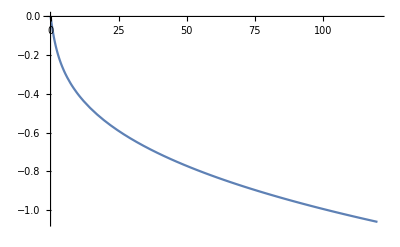

```mathematica
s3x=Plot[(-1.666676736466403*^34 ΔT-9.302686471020136*^33 Root[-1.666676736466403*^34 ΔT+1.731730866143749*^35 #1+1.5226090250626957*^36 #1^3&,1])/(1.8247577308539504*^35+1.5226090250626957*^36 Root[-1.666676736466403*^34 ΔT+1.731730866143749*^35 #1+1.5226090250626957*^36 #1^3&,1]^2),{ΔT,0,120}]
```

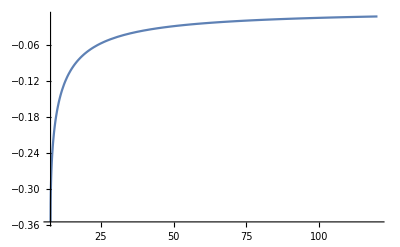

```mathematica
s2x= Plot[(3.41479454240454*^28 ΔT+0.06689194487264087 √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2))/(1.85861773321361*^28-1.2689146717396477*^28 ΔT^2-1. ΔT √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2)),{ΔT,7.771226149098018,120.0}, PlotRange->All]
```

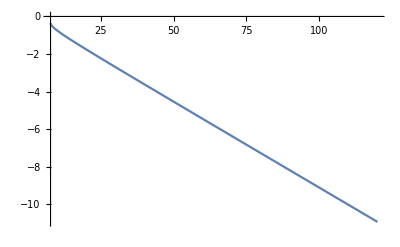

```mathematica
s1x=Plot[(3.41479454240454*^28 ΔT-0.06689194487264087 √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2))/(1.85861773321361*^28-1.2689146717396477*^28 ΔT^2+1. ΔT √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2)),{ΔT,7.771226149098018,120.0}]
```

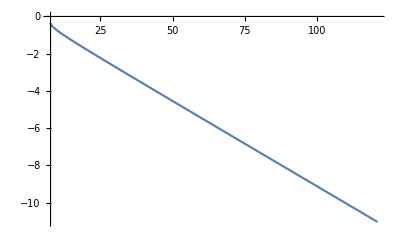

```mathematica
Plot[(3.41479454240454*^28 ΔT-0.06689194487264087 √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2))/(1.85861773321361*^28-1.2689146717396477*^28 ΔT^2+1. ΔT √(-9.723977220038575*^57+1.6101444441561384*^56 ΔT^2)),{ΔT,7.771226149098018,120.8618}]
```

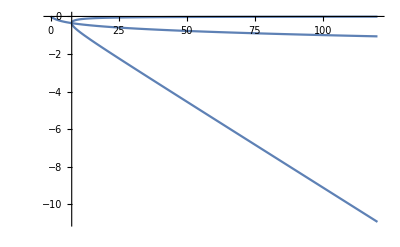

```mathematica
Show[s1x,s2x,s3x, PlotRange-> All]
```

```mathematica
s1x=Plot[soln[[1,1,2]],{ΔT,0,7.771226149098018}]
```

-Graphics-

```mathematica
soln[[1,1,2]]
```

ConditionalExpression[(3.41479×10^28 ΔT-0.0668919 √(-9.72398×10^57+1.61014×10^56 ΔT^2))/(1.85862×10^28-1.26891×10^28 ΔT^2+1. ΔT √(-9.72398×10^57+1.61014×10^56 ΔT^2)),ΔT>7.77123||ΔT<-7.77123]

```mathematica
s1x=Plot[soln[[1,1,2]],{η,0,5}]
```

```mathematica
wsol
```

```mathematica
kxx2 = soln[[1,1,2]];  kyy2 = soln[[1,2,2]]; kxy2 = soln[[1,3,2]];
```

```mathematica
kvec3 ={{kxx+ kxx2},{kyy+ kyy2},{kxy+ kxy2}};
```

```mathematica
Dm0 = Integrate[Q0m*z^2,{z,t,t + tm}]//Simplify;
```

```mathematica
(*Actuation*)

(*e2 = (zm*kvec)/.soln[[1]]; 

σm03 = Q0m.(e3 - eV1- e2) ;
σm903 = Q90m.(e3 - eV2- e2) ;*)

EnMFCS3=Am*(Integrate[Transpose[σm0].(zm*kvec)/2, {zm,t,tm+t}])//Expand//Simplify;
```

```mathematica
U3=0.5*Transpose[Nvec].Astar0.Nvec + 0.5*Transpose[kvec3].Dstar0.kvec3 /. {ψ-> ψ00, g-> kvec3[[1]]*kvec3[[2]]-kvec3[[3]]*kvec3[[3]]}//Expand// Rationalize//Simplify;
Utot=Integrate[U3,{x,y}∈Disk[{0,0},{a,b}]]//Rationalize//Expand//Simplify;
Utot2= Utot + EnMFCS;
```

```mathematica
soln=NSolve[{eq1==0 &&eq2==0&&eq3==0},{kxx,kyy,kxy},Reals]//Simplify
```

{{kxx→-4.40198,kyy→0.0752196,kxy→0.},{kxx→-0.0752196,kyy→4.40198,kxy→0.},{kxx→-1.0175,kyy→1.0175,kxy→0.}}

```mathematica
wsol1= 0.5*(kxx*x^2 + kyy*y^2) + kxy*x*y/.soln[[1]];
wsol2=0.5*(kxx*x^2 + kyy*y^2) + kxy*x*y/.soln[[2]];
```

```mathematica
wsol2/.{x-> 0, y-> b}
```

0.0136862

```mathematica
wsol1/.{x-> a, y-> 0}
```

-0.0307938

```mathematica
DensityPlot[wsol1, {x,y}∈Disk[{0,0},{a,b}], AspectRatio->Automatic, ColorFunction->"Rainbow",PlotLegends->Automatic, FrameLabel->{x,y},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->12],PlotPoints->200]
```

-Graphics-

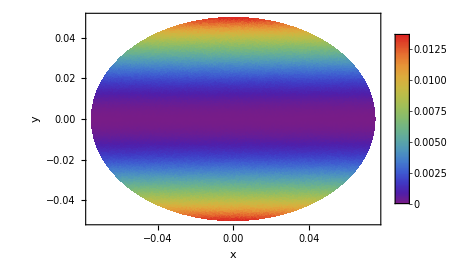

```mathematica
DensityPlot[wsol2, {x,y}∈Disk[{0,0},{a,b}], AspectRatio->Automatic, ColorFunction->"Rainbow",PlotLegends->Automatic, FrameLabel->{x,y},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->12],PlotPoints->100]
```

```mathematica
DensityPlot[wsol1, {x,y}∈Disk[{0,0},{a,b}], AspectRatio->Automatic, ColorFunction->"Rainbow",PlotLegends->Automatic, FrameLabel->{x,y},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->12],PlotPoints->200]
```

-Graphics-

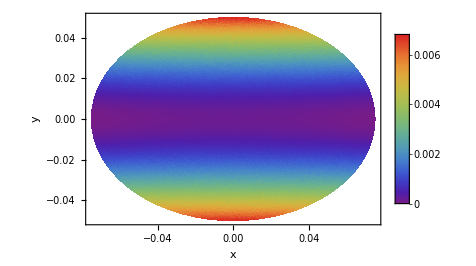

```mathematica
DensityPlot[wsol2, {x,y}∈Disk[{0,0},{a,b}], AspectRatio->Automatic, ColorFunction->"Rainbow",PlotLegends->Automatic, FrameLabel->{x,y},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->12],PlotPoints->100]
```

```mathematica
Export["shape2contourst2.pdf",%269,"PDF","AllowRasterization"->False]
```

shape2contourst2.pdf

```mathematica
Export["shapecontourst2.pdf",%274,"PDF","AllowRasterization"->False]
```

shapecontourst2.pdf

```mathematica
Dstar0//MatrixForm
```

(0.0819838 | 0.00417957 | 0
0.00417957 | 0.0819838 | 0
0 | 0 | 0.014555)

```mathematica
Nx=s*(x^2+(3 a^2*y^2)/b^2-a^2)/.{s-> s0}/.{g-> kxx*kyy-kxy*kxy}/.soln[[2]];
Ny=s*(y^2+(3 b^2*x^2)/a^2-b^2)/.{s-> s0}/.{g-> kxx*kyy-kxy*kxy}/.soln[[2]];;
Nxy=-2*s*x*y/.{s-> s0}/.{g-> kxx*kyy-kxy*kxy}/.soln[[2]];;
```

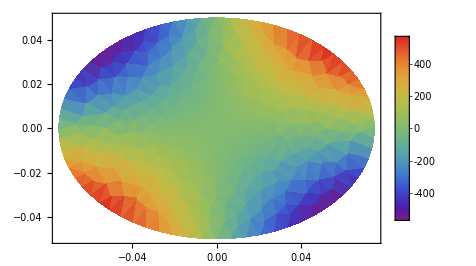

```mathematica
DensityPlot[Nxy, {x,y}∈Disk[{0,0},{a,b}], AspectRatio->Automatic, ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
ListDensityPlot[nyyplot,InterpolationOrder-> 6,ColorFunction->"Rainbow",ColorFunctionScaling->True,Frame->True,FrameStyle->BlackFrame,FrameTicks->{{With[{ticks=Range[-0.1,0.1,0.05]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[-0.1,0.1,0.05]},Thread[{ticks,[ticks,"DisplayStyle"->False]}]],None}},FrameLabel->MaTeX/@{"x \\,[m]","y \\, [m]"},PlotLegends->BarLegend[{"Rainbow",{-8024.3,26784.4}},Ticks->With[{tcks=Range[-8000,25000,5000]},Thread[{tcks,MaTeX[tcks,"DisplayStyle"->True]}]]],ClippingStyle->ColorData[{"Rainbow",{-1,1}}]/@{-1,1}]
```

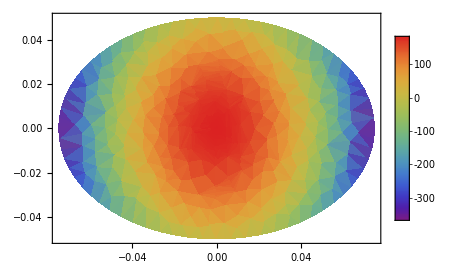

```mathematica
DensityPlot[Ny, {x,y}∈Disk[{0,0},{a,b}], AspectRatio->Automatic, ColorFunction->"Rainbow",PlotLegends->Automatic]
```

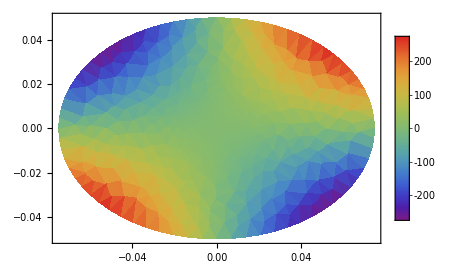

```mathematica
DensityPlot[Nxy, {x,y}∈Disk[{0,0},{a,b}], AspectRatio->Automatic, ColorFunction->"Rainbow",PlotLegends->Automatic]
```